30

ⅇ^(ⅈ (0.8+0.3 x))

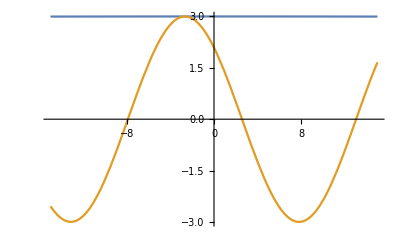

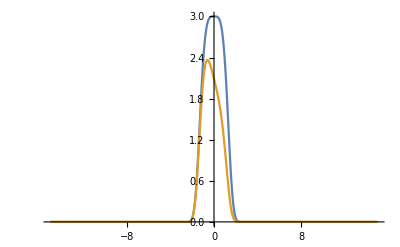

```mathematica
amp = 3;
width =300;
phase =0.8;
lin = 0.3;
chirp = 0;
supwidth=1;

domain = 30
totPhase[x_] = Exp[I(phase+lin*x+chirp*x^2)]
secpulse[x_] = (amp*totPhase[x])/Cosh[x/width];
supgauss[x_]=amp*totPhase[x]*Exp[-x^2/(2 width^2)-x^4/(4 supwidth^4)];

Plot[{Abs[secpulse[x]],Re[secpulse[x]]},{x,-domain/2,domain/2},PlotRange->All]
Plot[{Abs[supgauss[x]],Re[supgauss[x]]},{x,-domain/2,domain/2},PlotRange->All]
```